# Energy bands and gaps: The Kronig–Penney model

## Derivation of the Dispersion relation E(k)

Why the existence of separated energy bands and band gaps in a solid? 

The Kronig-Penney model is a quantum mechanical model used to describe the behavior of electrons in a one-dimensional periodic potential, often used to study band structures in solid-state physics. Solving it in Mathematica involves setting up the Schrödinger equation for a periodic potential, applying Bloch’s theorem, and numerically or analytically solving for the energy bands.

```mathematica
(*Some math, solving SE and impossing boundary condition around the delta potential located at x=0*)
```

```mathematica
Quit
```

The Kronig-Penney model uses a periodic array of delta-function potentials

The time-independent Schrödinger equation is:



the potential is zero everywhere except at x=0,where it is infinite but integrates to a finite value.


For solving the Schrodingee equation, we integrate very close to zero:


The term in the integrant shrinks to zero and the potential term is equal to . Using integration by parts for the kinetic term:



and taking the limit to :



The wavefunction between delta potentials is a plane wave (free particle solution):



where  (for E>0).

Near :

- To the left (x<0): ,

so.

- To the right (x>0):.

At (x=0):

   (continuity of  ).

 ,.

Substitute into the boundary condition:

```mathematica
(*After this, we get a set of equations, lets solve it in Mathematica*)
```

```mathematica
(*Define the wave functions*)
```

```mathematica
Quit
```

```mathematica
(*Assumptions*)
$Assumptions=Element[{m,eN,hbar,V0,A1,B1,A2,B2,k0,x,a},Reals]&&m>0&&a>0&&k0>0;
```

```mathematica
(*Wavefunctions at points of V=0*)

psifree1[x_]:=A1*Exp[I*k0*x]+B1*Exp[-I*k0*x];
psifree2[x_]:=A2*Exp[I*k0*x]+B2*Exp[-I*k0*x];
```

```mathematica
(*Derivatives*)

dpsifree1[x_]:=D[psifree1[x],x];
dpsifree2[x_]:=D[psifree2[x],x];

(*Evaluate derivatives at specific points*)

dpsifree10:=dpsifree1[x]/. x->0;
dpsifree20:=dpsifree2[x]/. x->0;
dpsifree2a:=dpsifree2[x]/. x->a;
dpsifree1a:=dpsifree1[x]/. x->a;
```

```mathematica
(*Boundary conditions*)

eq1=psifree1[0]==psifree2[0] 
(*Continuity at x=0*)
eq2=(hbar^2/(2*m)) (dpsifree2[x]-dpsifree1[x])==-a*V0*psifree1[x] /.x->0
(*Delta potential condition. This equation can be change it depending if you need to study repulsive or attractive model, for repulsive the rhs is + and attractive the rhs is negative*)
eq3=psifree2[a]==Exp[I*k*a]*psifree1[x]/.x->0 
(*Bloch condition for wavefunction*)
eq4=dpsifree2[a]==Exp[I*k*a]*dpsifree1[x]/.x->0
(*Bloch condition for derivative*)
```

A1+B1==A2+B2

(hbar^2 (-ⅈ A1 k0+ⅈ A2 k0+ⅈ B1 k0-ⅈ B2 k0))/(2 m)==-a (A1+B1) V0

B2 ⅇ^(-ⅈ a k0)+A2 ⅇ^(ⅈ a k0)==(A1+B1) ⅇ^(ⅈ a k)

-ⅈ B2 ⅇ^(-ⅈ a k0) k0+ⅈ A2 ⅇ^(ⅈ a k0) k0==ⅇ^(ⅈ a k) (ⅈ A1 k0-ⅈ B1 k0)

```mathematica
equations={eq1,eq2,eq3,eq4};
```

```mathematica
(*Compute the coefficient matrix, I tried to solve it but it gave me trivial solution so we better impose non trivial solution*)


coeffMatrix=CoefficientArrays[equations,{A1,B1,A2,B2}][[2]];
```

```mathematica
dispersionRelation=Det[coeffMatrix]==0
```

(2 hbar^2 k0^2)/m+(2 ⅇ^(2 ⅈ a k) hbar^2 k0^2)/m-(2 ⅇ^(ⅈ a k-ⅈ a k0) hbar^2 k0^2)/m-(2 ⅇ^(ⅈ a k+ⅈ a k0) hbar^2 k0^2)/m+2 ⅈ a ⅇ^(ⅈ a k-ⅈ a k0) k0 V0-2 ⅈ a ⅇ^(ⅈ a k+ⅈ a k0) k0 V0==0

```mathematica
dispersionRelation//ExpToTrig//FullSimplify
```

hbar^2 k0 (Cos[a k]-Cos[a k0])+a m V0 Sin[a k0]==0

```mathematica
Ekrepulsive potential=hbar^2 k0 (Cos[a k]-Cos[a k0])==a m V0 Sin[a k0]
```

```mathematica
(*This solution is for a repulsive potential*)
```

```mathematica
Ekattractivepotential=hbar^2 k0 (Cos[a k]-Cos[a k0])==-a m V0 Sin[a k0]
```

```mathematica
(*This solution is for an attractive potential*)
```

## Plotting the First band

```mathematica
(*Now lets plot the dispersion relation, here is a bit tricky because the dispersion relation is a trascendental equation, so we better solve this numerically*)
```

```mathematica
Quit
```

```mathematica
(*Constants*)
hbar=1;
a=1;
m=1;
V0=1;

(*Equation*)
eqn[k_,k0_]:=hbar^2 k0 (Cos[a k]-Cos[a k0])-a m V0 Sin[a k0];
```

```mathematica
bandData=Reap[Module[{prevK0=1},Do[Module[{sols,realSols,filteredSols,closest,energy},sols=NSolve[{eqn[k,k0]==0,-2 Pi/a<k0<2 Pi/a},k0,Reals];
realSols=k0/. sols;
filteredSols=Sort[Select[realSols,Abs[#]>0.01&]];
If[filteredSols=!={},closest=filteredSols[[Ceiling[Length[filteredSols]/2]]];
(*pick middle root*)prevK0=closest;
energy=hbar^2 closest^2/(2 m);
Sow[{k,energy}];];],{k,-Pi/a,Pi/a,0.01}]]][[2,1]];
```

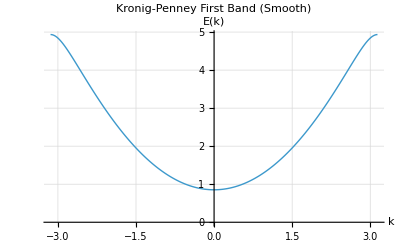

```mathematica
ListLinePlot[bandData,PlotStyle->Thick,AxesLabel->{"k","E(k)"},PlotLabel->"Kronig-Penney First Band (Smooth)",GridLines->Automatic]
```

```mathematica
(*In this code values of k in the interval or -pi/a to pi/a are tested, for each value of k we get a set of values between the range of k0, these are the bands, then we order them from lowest to highest, creating the bands.*)
```

```mathematica
Do[sols=NSolve[{eqn[k,k0]==0,-2 Pi/a<k0<2 Pi/a},k0,Reals];
realSols=k0/. sols;
Print["k = ",k,", real roots = ",realSols];,{k,-Pi/a,Pi/a,0.5}];
```

k = -3.14159, real roots = {-3.67319,-3.14159,0.,3.14159,3.67319}

k = -2.64159, real roots = {-3.9435,-2.88225,0.,2.88225,3.9435}

k = -2.14159, real roots = {-4.38197,-2.47905,0.,2.47905,4.38197}

k = -1.64159, real roots = {-4.84653,-2.08232,0.,2.08232,4.84653}

k = -1.14159, real roots = {-5.31955,-1.72719,0.,1.72719,5.31955}

k = -0.641593, real roots = {-5.79326,-1.45289,0.,1.45289,5.79326}

k = -0.141593, real roots = {-6.22972,-1.31405,0.,1.31405,6.22972}

k = 0.358407, real roots = {-6.05433,-1.35393,0.,1.35393,6.05433}

k = 0.858407, real roots = {-5.58842,-1.55868,0.,1.55868,5.58842}

k = 1.35841, real roots = {-5.11388,-1.87393,0.,1.87393,5.11388}

k = 1.85841, real roots = {-4.64352,-2.25107,0.,2.25107,4.64352}

k = 2.35841, real roots = {-4.18637,-2.656,0.,2.656,4.18637}

k = 2.85841, real roots = {-3.78123,-3.03703,0.,3.03703,3.78123}

## Plotting more bands

```mathematica
Quit
```

```mathematica
(*Constants*)
hbar=1;
a=1;
m=1;
V0=8;

(*when the last term is negative, we are dealing with repulsive potential*)
eqn[k_,k0_]:=hbar^2 k0 (Cos[a k]-Cos[a k0])-a m V0 Sin[a k0];

(*Number of bands*)
numBands=10;

(*Initialize band containers*)
bandData=Table[{},{numBands}];

Do[
Module[{sols,realSols,sortedSols,energies},sols=NSolve[{eqn[k,k0]==0,-20<k0<20},k0,Reals];
realSols=Select[k0/. sols,Abs[#]>0.01&];(*discard trivial root*)sortedSols=SortBy[realSols,#^2&];(*sort by energy*)energies=hbar^2 #^2/(2 m)&/@sortedSols;
Do[If[i<=Length[energies],AppendTo[bandData[[i]],{k,energies[[i]]}]],{i,1,numBands}];],{k,-Pi/a,Pi/a,0.01}];
```

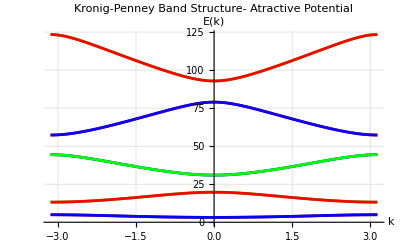

```mathematica
ListLinePlot[bandData,PlotStyle->{Red,Blue,Green},AxesLabel->{"k","E(k)"},PlotLabel->"Kronig-Penney Band Structure- Atractive Potential",GridLines->Automatic]
```